```mathematica
ClearAll;
```

```mathematica
thetaL=60 Degree;
gl=0.3;
gψV=gl/6 (3 Cos[thetaL]^2-1);
gfV=1;
Ncf=1;
GammaZp =0.1;
sigmaV[MDM_,MZp_]:= (Ncf*MDM^2*gψV^2*gfV^2)/(Pi ((4*MDM^2-MZp^2)^2+MZp^2*GammaZp^2));
sigmaV1=10^-9;
```

```mathematica
g=2;
gst=106.75;
MPl=1.2*10^19;
Hub[X_,MDM_]:=1.66*Sqrt[gst]*MDM^2/(X*MPl);
YDMeq[X_]:= 0.0382402*(g/Sqrt[gst])*MPl*10*X^(3/2)*Exp[-X];
YDMeq[50]
```

0.0605729

```mathematica
Ys=NDSolve[{YDM'[X]==-sigmaV1/X^2(YDM[X]^2-YDMeq[X]^2),YDM[1]==N[YDMeq[1]]},YDM,{X,1,50}]
```

{{YDM→InterpolatingFunction[…]}}

```mathematica
Yn=NDSolve[{YDM'[X]==-sigmaV1/X^2(YDM[X]^2-YDMeq[X]^2),YDM[50]==Evaluate[YDM[50] /.Ys]},YDM,{X,50,1000}]
```

{{YDM→InterpolatingFunction[…]}}

```mathematica
ga=LogLogPlot[({YDM[X] /.Ys})/(YDMeq[1]),{X,1,50}(*,BaseStyle->{FontFamily->"Times",FontSize->10}*),AxesLabel->{HoldForm[X],HoldForm["Y/Y(1)"]},PlotStyle->{RGBColor[0.2,0.2,0.2],Thickness[0.004]},PlotRange->{{1,300},{10,10^-11}},Frame->True,FrameStyle->Thickness[0.005](*Darker[Black]*),FrameLabel->{Style["x",Darker[Black],15],Style["Y/(Y (x = 1))",Darker[Black],13]},GridLines->{{18},{}},GridLinesStyle->Directive[Dashed,Darker[Black],Thickness[0.0009]],LabelStyle->Directive[Darker[Black]],Epilog->{Inset[Style["x_f",Darker[Black],16],Scaled[{0.54,0.94}]],Inset[Style["Y_today",Darker[Black],14],Scaled[{0.92,0.26}]],Inset[Style["Y_(eq^m)",Darker[Black],14],Scaled[{0.65,0.07}]]}];
(*gYa=LogLogPlot[({YDM[X] /.Ys}),{X,1,50},BaseStyle->{FontFamily->"Times",FontSize->10},AxesLabel->{HoldForm[X],HoldForm["Y_DM"]},PlotStyle->{RGBColor[0.2,0.2,0.2],Dashed},PlotRange->{{1,300},Automatic}]*)
gb=LogLogPlot[({YDM[X] /.Yn})/(YDMeq[1]),{X,50,300},BaseStyle->{FontFamily->"Times",FontSize->10},AxesLabel->{HoldForm[X],HoldForm["Y/Y(1)"]},PlotStyle->{RGBColor[0.2,0.2,0.2],Thickness[0.004]},PlotRange->{{1,300},{10,10^-11}}];
```

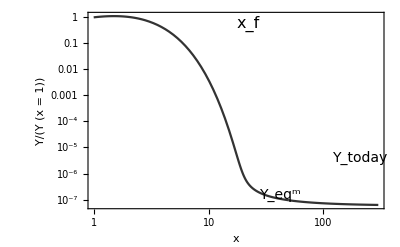

```mathematica
g1=Show[ga,gb]
(*Show[ga]
Show[gb]*)
```

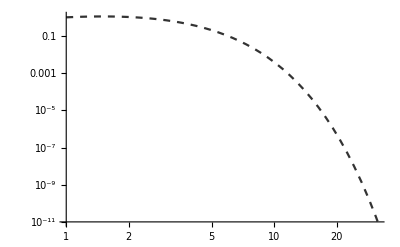

```mathematica
geq=LogLogPlot[YDMeq[X]/YDMeq[1],{X,1,50},PlotStyle->{RGBColor[0.2,0.2,0.2],Dashed,Thickness[0.004]},PlotRange->{{1,300},{10,10^-11}}]
```

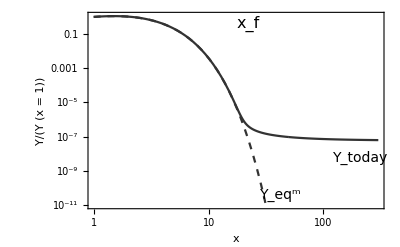

```mathematica
g2=Show[ga,gb,geq]
```

```mathematica
SetDirectory["/home/utkarsh/Dropbox/Utkarsh_PhD/Relic Density Mathcode/"];
Export["boltzmann_solution1.pdf",g2]
```

boltzmann_solution1.pdf

```mathematica
(*p1=LogLogPlot[({YDM[X]/.Ys})/(YDMeq[1]),{X,1,50}]       {{1,300},{0,10^-15}}*)
```

```mathematica
alphaL1 =gL1^2/(4 Pi);
thetaL= x Degree;

gpsiV=gL2/6(3 Cos[thetaL]^2 -1);
(3 Cos[126.471 Degree]^2 -1)
s1=Solve[alphaL1==0.001,gL1]
gL2=0.001;s2=Solve[gpsiV==0.1,x]
```